# 量子力学变分法近似

```mathematica
H[ψ_]:=h^2/(2m )*D[ψ,{x,2}]+V[x]
```

```mathematica
ϕ[x_]:=A Exp[-b x^2]/.{A->Sqrt[b/Pi]}
```

```mathematica
Integrate[ϕ[x],{x,-Infinity,Infinity},Assumptions->b>0]
```

1

```mathematica
ϕ[x]
```

(√b ⅇ^(-b x^2))/(√π)

```mathematica
first=Integrate[ϕ[x]*(H[ϕ[x]])/.{V[x]->α Abs[x]},{x,-Infinity,Infinity},Assumptions->b>0&&α<0]
```

(-√2 b^2 h^2+4 m α)/(4 √b m √π)

```mathematica
Refine[Minimize[first,b],α<0&&b>0&&h>0&&m>0]
```

{-∞,{b→Indeterminate}}

```mathematica
second=Integrate[ϕ[x]*(H[ϕ[x]])/.{V[x]->α x^4},{x,-Infinity,Infinity},Assumptions->b>0&&α<0]
```

-(b^(3/2) h^2)/(2 m √(2 π))+(3 α)/(4 b^2)

```mathematica
Refine[Minimize[second,{b}],{α<0,m>0,h>0}]
```

{-∞,{b→Indeterminate}}

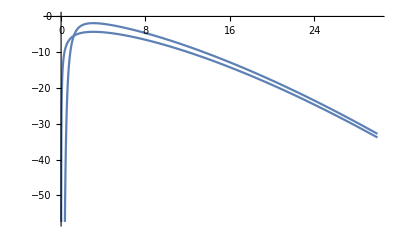

```mathematica
Plot[{second,first}/.{h->1,m->1,α->-10},{b,-1,30}]
```

```mathematica
ϕ[x_]:=A/(x^2+b^2)
```

```mathematica
Integrate[ϕ[x],{x,-Infinity,Infinity},Assumptions->b>0]
```

1

```mathematica
ϕ[x_]:=A/(x^2+b^2)/.{A->b/Pi}
```

```mathematica
ϕ[x]
```

b/(π (b^2+x^2))

```mathematica
third=Integrate[ϕ[x]*(H[ϕ[x]])/.{V[x]->1/2 m ω^2 x^2},{x,-Infinity,Infinity},Assumptions->b>0&&ω>0&&m>0]
```

Integrate::idiv: -(b^4 h^2)/(m π^2 (b^2+x^2)^4)+(3 b^2 h^2 x^2)/(m π^2 (b^2+x^2)^4)+(b m x^2 ω^2)/(2 π (b^2+x^2)) 的积分在 {-∞,∞} 上不收敛.

Integrate[(b ((b h^2 ((8 x^2)/((b^2+x^2)^3)-2/((b^2+x^2)^2)))/(2 m π)+1/2 m x^2 ω^2))/(π (b^2+x^2)),{x,-∞,∞},Assumptions→b>0&&ω>0&&m>0]